# Sistemi Meccanici e Modelli Homework 2- Anno Accademico 2022-23

## Istruzioni (aggiornate 25/10/22) Stefano Tonini 218722 stefano.tonini-2@studenti.unitn.it

### Svolgimento dell’homework

Sviluppare gli argomenti indicati  e produrre un notebook Mathematica documentato che, per ogni punto, illustri:
a) Gli elementi di teoria utilizzati.
b) Lo svolgimento e i risultati.

Indicare: nome, matricola e la e-mail.
Data di consegna dell’elaborato: 21/11/22.

### Modalità di esame

Le modalità d’esame previste nel Syllabus sono riportate di seguito:

#### Metodi didattici e attività di apprendimento richieste allo studente

(...). Si assegneranno 3 homework per lo svolgimento individuale a casa. Gli homework consistono nella risoluzione di problemi di media complessità, applicando gli elementi appresi durante il corso.
Una licenza personale di Wolfram Mathematica sarà data ad ogni studente. Durante il corso Wolfram Mathematica sarà utilizzato per creare e analizzare modelli matematici di vari sistemi meccanici con i metodi teorici indicati sopra. Mathematica sarà inoltre necessaria per lo svolgimento dei 3 homework.

(...).Three homeworks will be assigned for individual study. The homeworks consist of solving problems of medium complexity, applying the elements learned in the course.
A personal Wolfram Mathematica license will be given to each student. During the course Wolfram Mathematica will be used to create and analyze mathematical models of various mechanical systems using the theoretical methods outlined above. Mathematica will also be required for the execution of the 3 homeworks.

#### Metodo di accertamento e criteri di valutazione

L‘esame è composto di una prova scritta e dei 3 homework. 
Lo scritto è composto di una o più brevi domande di teoria e/o esercizi. Seguirà una correzione dello scritto e degli homework nella quale il docente potrà chiedere chiarimenti sugli elaborati. La correzione verrà svolta per appuntamento individualmente su Zoom.
Eventuali lacune su parti del programma non possono essere colmate rispondendo a domande aggiuntive su altre parti del programma. Qualora fosse acclarata una preparazione con lacune l’esame non può essere superato. Per esempio, costituiscono gravi lacune la incapacità di scrivere le equazioni della cinematica e della dinamica con uno dei metodi spiegati a lezione (per esempio la incapacità di scrivere ed applicare le equazioni di Newton-Eulero).
Il voto viene attribuito attraverso un giudizio complessivo sulla prova e sulla discussione degli homework svolti (tutti gli homework saranno stati corretti ma la valutazione resta riservata fino all’esame). In particolare la prova scritta vale fino a 18 punti e gli homework fino 4 punti ciascuno. E’ possibile fare l’esame senza uno o più homework, ma il voto sarà ridotto in proporzione a quanto non è stato consegnato.
Lo svolgimento degli homework, entro le scadenze assegnate, è obbligatorio.  I primi due homework hanno scadenza fissa per tutti gli studenti. L’ultimo homework potrà essere consegnato una settima prima dell’esame (e non oltre l’appello di settembre).

The examination consists of a written test and the 3 homework papers. 
The written consists of one or more short theory questions and/or exercises. This will be followed by a correction of the written part and homeworks in which the lecturer may ask for clarification of the papers. The correction will be done by appointment individually on Zoom.
Any gaps on parts of the syllabus cannot be filled by answering additional questions on other parts of the syllabus. If preparation with gaps is established, the exam cannot be passed. For example, the inability to write the equations of kinematics and dynamics by any of the methods explained in class (e.g., the inability to write and apply the Newton-Euler equations) constitute serious gaps.
The grade is awarded through an overall judgment on the proof and discussion of the homework done (all homework will have been corrected but the grade remains confidential until the exam). Specifically, the written test is worth up to 18 points and the homework up to 4 points each. It is possible to take the exam without one or more homework, but the grade will be reduced in proportion to what was not handed in.
Doing the homework, within the assigned deadlines, is mandatory. The first two homeworks have fixed deadlines for all students. The last homework may be turned in one week before the exam (and no later than the September roll call).

## Dinamica del trabucco

Si consideri il trabucco mostrato in figura. Le principali caratteristiche geometriche ed inerziali sono annotate. Il baricentro G1 sta a metà della trave (1). I momenti di inerzia baricentrici sono I1 =1/12 m1 L^2 e  I2 = 1/12 m2 L2^2.

Il trabucco è un sistema ibrido, nel senso che ha due configurazioni distinte: 1) a sinistra, quando il proiettile m3 è appoggiato al suolo il sistema ha 2 gradi di libertà. In questa situazione m3 è soggetto alla reazione vincolare del suolo. Si suppone che ci sia attrito con il suolo e che sia fc il coefficiente di attrito cinetico; 2) a destra, quando il proiettile si alza da suolo, il trabucco ha 3 gradi di libertà, ma mancano le forze normale e di attrito del suolo.

Modellare la corda CD come un’asta senza massa (salvo verificare più tardi che non vada mai in compressione).

-Graphics-

Si richiede:

### a) Scrivere le equazioni del moto nelle due situazioni 1 e 2 sopra dette.

#### Equazioni del moto caso 1

```mathematica
(*2 Gradi di libertà*)
θ1= q1[t];
θ2=q2[t];
(*Momento dìinerzia del corpo 1 con polo A (con teorema Huygens-Steiner)*)
IA=I1+m1(L/2-L1)^2;
(*Coordinate dei punti A,B,C,D*)
xA=0;
yA=h;
xB=xA+L1 Cos[θ1];
yB=yA+L1 Sin[θ1];
xC=xA-(L-L1)Cos[θ1];
yC=yA-(L-L1)Sin[θ1];
xD=xC-L3 Cos[θ3[t]];
yD=yC-L3 Sin[θ3[t]];
```

```mathematica
(*Posizioni dei baricentri*)
xG1=xA-(L/2-L1)Cos[θ1];
yG1=yA-(L/2-L1)Sin[θ1];
xG2=xB+L2 Cos[θ2];
yG2=yB+L2 Sin[θ2];
xG3=xD;
yG3=yD;
```

```mathematica
(*Corpo 1*)
N1x=m1*D[xG1, t,t]==-R2x-R3 Cos[θ3[t]]+R1x;
N1y=m1*D[yG1, t,t]==-R2y-R3 Sin[θ3[t]]-m1*g+R1y;
E1=IA*D[θ1, t,t]==MAR2-MARC-MAm1g;
```

```mathematica
(*Corpo 2*)
N2x=m2*D[xG2, t,t]==R2x;
N2y=m2*D[yG2, t,t]==R2y-m2*g;
E2=I2*D[θ2, t,t]==-MG2R2;
```

```mathematica
(*Corpo 3*)
N3x=m3*D[xG3, t,t]==R3 Cos[θ3[t]]-N3*fc;
N3y=m3*D[yG3, t,t]==N3+R3 Sin[θ3[t]]-m3*g;
```

```mathematica
(*Calcolo i momenti delle forze*)
AB = L1 {Cos[θ1],Sin[θ1],0};
MAR2 = (AB×{R2x,R2y,0})[[3]]
```

L1 R2y Cos[q1[t]]-L1 R2x Sin[q1[t]]

```mathematica
AC=(L-L1) {Cos[θ1],Sin[θ1],0};
MARC= (AC×{R3 Cos[θ3[t]],R3 Sin[θ3[t]],0})[[3]]
```

-L R3 Cos[θ3[t]] Sin[q1[t]]+L1 R3 Cos[θ3[t]] Sin[q1[t]]+L R3 Cos[q1[t]] Sin[θ3[t]]-L1 R3 Cos[q1[t]] Sin[θ3[t]]

```mathematica
G2B = L2{Cos[θ2],Sin[θ2],0};
MG2R2 = (G2B ×{R2x,R2y,0})[[3]]
```

L2 R2y Cos[q2[t]]-L2 R2x Sin[q2[t]]

```mathematica
AG1 = (L/2-L1){Cos[θ1],Sin[θ1],0};
MAm1g =(AG1 ×{0,m1*g,0})[[3]]
```

1/2 g L m1 Cos[q1[t]]-g L1 m1 Cos[q1[t]]

```mathematica
(*Per la fase 2 bisogna modificare 2 variabili nelle equazioni di Newton-Eulero della fase 1. Si deve porre la normale del piano N3=0 ed inoltre aggiungere il terzo grado di libertà q3[t]*)
```

### b) Nel caso 1, determinare le reazioni vincolari, compresa la forza normale del suolo sulla massa m3, ed esplicitare due equazioni per i due gradi di libertà (osservazione: in contatto con il suolo, l’angolo θ3 dell’asta CD è determinato dalle equazioni di chiusura ed è quindi un cedente).

```mathematica
(*Espressioni delle reazioni vincolari per la fase 1*)
solR=Simplify@Solve[{N1x,N1y,N2x,N2y,N3x,N3y},{R1x,R1y,R2x,R2y,R3,N3}]
```

{{R1x→1/(2 (Cos[θ3[t]]+fc Sin[θ3[t]]))(2 fc g m3 Cos[θ3[t]]+(2 fc (L-L1) m3 Cos[θ3[t]] Sin[q1[t]]+Cos[q1[t]] ((-2 L1 (m1+m2+m3)+L (m1+2 m3)) Cos[θ3[t]]+fc (L m1-2 L1 (m1+m2)) Sin[θ3[t]])) q1'[t]^2-2 L2 m2 Cos[q2[t]] (Cos[θ3[t]]+fc Sin[θ3[t]]) q2'[t]^2+2 L3 m3 Cos[θ3[t]]^2 θ3'[t]^2+fc L3 m3 Sin[2 θ3[t]] θ3'[t]^2-2 fc L m3 Cos[q1[t]] Cos[θ3[t]] q1''[t]+2 fc L1 m3 Cos[q1[t]] Cos[θ3[t]] q1''[t]+L m1 Cos[θ3[t]] Sin[q1[t]] q1''[t]-2 L1 m1 Cos[θ3[t]] Sin[q1[t]] q1''[t]-2 L1 m2 Cos[θ3[t]] Sin[q1[t]] q1''[t]+2 L m3 Cos[θ3[t]] Sin[q1[t]] q1''[t]-2 L1 m3 Cos[θ3[t]] Sin[q1[t]] q1''[t]+fc L m1 Sin[q1[t]] Sin[θ3[t]] q1''[t]-2 fc L1 m1 Sin[q1[t]] Sin[θ3[t]] q1''[t]-2 fc L1 m2 Sin[q1[t]] Sin[θ3[t]] q1''[t]-2 L2 m2 Cos[θ3[t]] Sin[q2[t]] q2''[t]-2 fc L2 m2 Sin[q2[t]] Sin[θ3[t]] q2''[t]-2 fc L3 m3 Cos[θ3[t]]^2 θ3''[t]+L3 m3 Sin[2 θ3[t]] θ3''[t]),R1y→1/(2 (Cos[θ3[t]]+fc Sin[θ3[t]]))(2 g m1 Cos[θ3[t]]+2 g m2 Cos[θ3[t]]+2 fc g m1 Sin[θ3[t]]+2 fc g m2 Sin[θ3[t]]+2 fc g m3 Sin[θ3[t]]+((L m1-2 L1 (m1+m2)) Cos[θ3[t]] Sin[q1[t]]+(2 (L-L1) m3 Cos[q1[t]]+fc (-2 L1 (m1+m2+m3)+L (m1+2 m3)) Sin[q1[t]]) Sin[θ3[t]]) q1'[t]^2-2 L2 m2 Sin[q2[t]] (Cos[θ3[t]]+fc Sin[θ3[t]]) q2'[t]^2+2 fc L3 m3 Sin[θ3[t]]^2 θ3'[t]^2+L3 m3 Sin[2 θ3[t]] θ3'[t]^2-L m1 Cos[q1[t]] Cos[θ3[t]] q1''[t]+2 L1 m1 Cos[q1[t]] Cos[θ3[t]] q1''[t]+2 L1 m2 Cos[q1[t]] Cos[θ3[t]] q1''[t]-fc L m1 Cos[q1[t]] Sin[θ3[t]] q1''[t]+2 fc L1 m1 Cos[q1[t]] Sin[θ3[t]] q1''[t]+2 fc L1 m2 Cos[q1[t]] Sin[θ3[t]] q1''[t]-2 fc L m3 Cos[q1[t]] Sin[θ3[t]] q1''[t]+2 fc L1 m3 Cos[q1[t]] Sin[θ3[t]] q1''[t]+2 L m3 Sin[q1[t]] Sin[θ3[t]] q1''[t]-2 L1 m3 Sin[q1[t]] Sin[θ3[t]] q1''[t]+2 L2 m2 Cos[q2[t]] Cos[θ3[t]] q2''[t]+2 fc L2 m2 Cos[q2[t]] Sin[θ3[t]] q2''[t]+2 L3 m3 Sin[θ3[t]]^2 θ3''[t]-fc L3 m3 Sin[2 θ3[t]] θ3''[t]),R2x→-m2 (L1 Cos[q1[t]] q1'[t]^2+L2 Cos[q2[t]] q2'[t]^2+L1 Sin[q1[t]] q1''[t]+L2 Sin[q2[t]] q2''[t]),R2y→m2 (g-L1 Sin[q1[t]] q1'[t]^2-L2 Sin[q2[t]] q2'[t]^2+L1 Cos[q1[t]] q1''[t]+L2 Cos[q2[t]] q2''[t]),R3→1/(Cos[θ3[t]]+fc Sin[θ3[t]])m3 (fc g+(L-L1) (Cos[q1[t]]+fc Sin[q1[t]]) q1'[t]^2+L3 (Cos[θ3[t]]+fc Sin[θ3[t]]) θ3'[t]^2-fc L Cos[q1[t]] q1''[t]+fc L1 Cos[q1[t]] q1''[t]+L Sin[q1[t]] q1''[t]-L1 Sin[q1[t]] q1''[t]-fc L3 Cos[θ3[t]] θ3''[t]+L3 Sin[θ3[t]] θ3''[t]),N3→(m3 (g Cos[θ3[t]]+(L-L1) Sin[q1[t]-θ3[t]] q1'[t]^2-(L-L1) Cos[q1[t]-θ3[t]] q1''[t]-L3 θ3''[t]))/(Cos[θ3[t]]+fc Sin[θ3[t]])}}

```mathematica
Simplify@Solve[{E1,E2},{q1''[t],q2''[t]}]/.solR
```

{{{q1''[t]→1/(4 I1+(L-2 L1)^2 m1)(Cos[q1[t]] (-2 g (L-2 L1) m1+4 L1 m2 (g-L1 Sin[q1[t]] q1'[t]^2-L2 Sin[q2[t]] q2'[t]^2+L1 Cos[q1[t]] q1''[t]+L2 Cos[q2[t]] q2''[t]))-4 (-L1 m2 Sin[q1[t]] (L1 Cos[q1[t]] q1'[t]^2+L2 Cos[q2[t]] q2'[t]^2+L1 Sin[q1[t]] q1''[t]+L2 Sin[q2[t]] q2''[t])+1/(Cos[θ3[t]]+fc Sin[θ3[t]])(-L+L1) m3 Sin[q1[t]-θ3[t]] (fc g+(L-L1) (Cos[q1[t]]+fc Sin[q1[t]]) q1'[t]^2+L3 (Cos[θ3[t]]+fc Sin[θ3[t]]) θ3'[t]^2-fc L Cos[q1[t]] q1''[t]+fc L1 Cos[q1[t]] q1''[t]+L Sin[q1[t]] q1''[t]-L1 Sin[q1[t]] q1''[t]-fc L3 Cos[θ3[t]] θ3''[t]+L3 Sin[θ3[t]] θ3''[t]))),q2''[t]→1/I2(-L2 m2 Cos[q2[t]] (g-L1 Sin[q1[t]] q1'[t]^2-L2 Sin[q2[t]] q2'[t]^2+L1 Cos[q1[t]] q1''[t]+L2 Cos[q2[t]] q2''[t])-L2 m2 Sin[q2[t]] (L1 Cos[q1[t]] q1'[t]^2+L2 Cos[q2[t]] q2'[t]^2+L1 Sin[q1[t]] q1''[t]+L2 Sin[q2[t]] q2''[t]))}}}

```mathematica
E2GdL= Simplify[{E1,E2}/.solR]
```

{{1/2 g L m1 Cos[q1[t]]+(I1+1/4 (L-2 L1)^2 m1) q1''[t]+1/(Cos[θ3[t]]+fc Sin[θ3[t]])L1 m3 Cos[θ3[t]] Sin[q1[t]] (fc g+(L-L1) (Cos[q1[t]]+fc Sin[q1[t]]) q1'[t]^2+L3 (Cos[θ3[t]]+fc Sin[θ3[t]]) θ3'[t]^2-fc L Cos[q1[t]] q1''[t]+fc L1 Cos[q1[t]] q1''[t]+L Sin[q1[t]] q1''[t]-L1 Sin[q1[t]] q1''[t]-fc L3 Cos[θ3[t]] θ3''[t]+L3 Sin[θ3[t]] θ3''[t])+1/(Cos[θ3[t]]+fc Sin[θ3[t]])L m3 Cos[q1[t]] Sin[θ3[t]] (fc g+(L-L1) (Cos[q1[t]]+fc Sin[q1[t]]) q1'[t]^2+L3 (Cos[θ3[t]]+fc Sin[θ3[t]]) θ3'[t]^2-fc L Cos[q1[t]] q1''[t]+fc L1 Cos[q1[t]] q1''[t]+L Sin[q1[t]] q1''[t]-L1 Sin[q1[t]] q1''[t]-fc L3 Cos[θ3[t]] θ3''[t]+L3 Sin[θ3[t]] θ3''[t])==g L1 m1 Cos[q1[t]]+L1 m2 Cos[q1[t]] (g-L1 Sin[q1[t]] q1'[t]^2-L2 Sin[q2[t]] q2'[t]^2+L1 Cos[q1[t]] q1''[t]+L2 Cos[q2[t]] q2''[t])+L1 m2 Sin[q1[t]] (L1 Cos[q1[t]] q1'[t]^2+L2 Cos[q2[t]] q2'[t]^2+L1 Sin[q1[t]] q1''[t]+L2 Sin[q2[t]] q2''[t])+1/(Cos[θ3[t]]+fc Sin[θ3[t]])L m3 Cos[θ3[t]] Sin[q1[t]] (fc g+(L-L1) (Cos[q1[t]]+fc Sin[q1[t]]) q1'[t]^2+L3 (Cos[θ3[t]]+fc Sin[θ3[t]]) θ3'[t]^2-fc L Cos[q1[t]] q1''[t]+fc L1 Cos[q1[t]] q1''[t]+L Sin[q1[t]] q1''[t]-L1 Sin[q1[t]] q1''[t]-fc L3 Cos[θ3[t]] θ3''[t]+L3 Sin[θ3[t]] θ3''[t])+1/(Cos[θ3[t]]+fc Sin[θ3[t]])L1 m3 Cos[q1[t]] Sin[θ3[t]] (fc g+(L-L1) (Cos[q1[t]]+fc Sin[q1[t]]) q1'[t]^2+L3 (Cos[θ3[t]]+fc Sin[θ3[t]]) θ3'[t]^2-fc L Cos[q1[t]] q1''[t]+fc L1 Cos[q1[t]] q1''[t]+L Sin[q1[t]] q1''[t]-L1 Sin[q1[t]] q1''[t]-fc L3 Cos[θ3[t]] θ3''[t]+L3 Sin[θ3[t]] θ3''[t]),I2 q2''[t]==-L2 m2 (g Cos[q2[t]]-L1 Sin[q1[t]-q2[t]] q1'[t]^2+L1 Cos[q1[t]-q2[t]] q1''[t]+L2 q2''[t])}}

```mathematica
(*2 equazioni differenziali per i 2 gradi di libertà del sistema*)
solGdL=Simplify@Solve[{E2GdL[[1,1]],E2GdL[[1,2]]},{q1''[t],q2''[t]}]
```

{{q1''[t]→-((L1 L2^2 m2^2 Cos[q1[t]-q2[t]] (g Cos[q2[t]]-L1 Sin[q1[t]-q2[t]] q1'[t]^2)-1/(2 (Cos[θ3[t]]+fc Sin[θ3[t]]))(I2+L2^2 m2) (-g L m1 Cos[q1[t]] Cos[θ3[t]]+2 g L1 m1 Cos[q1[t]] Cos[θ3[t]]+2 g L1 m2 Cos[q1[t]] Cos[θ3[t]]+2 fc g L m3 Cos[θ3[t]] Sin[q1[t]]-2 fc g L1 m3 Cos[θ3[t]] Sin[q1[t]]-fc g L m1 Cos[q1[t]] Sin[θ3[t]]+2 fc g L1 m1 Cos[q1[t]] Sin[θ3[t]]+2 fc g L1 m2 Cos[q1[t]] Sin[θ3[t]]-2 fc g L m3 Cos[q1[t]] Sin[θ3[t]]+2 fc g L1 m3 Cos[q1[t]] Sin[θ3[t]]+2 (L-L1)^2 m3 (Cos[q1[t]]+fc Sin[q1[t]]) Sin[q1[t]-θ3[t]] q1'[t]^2+2 L1 L2 m2 Sin[q1[t]-q2[t]] (Cos[θ3[t]]+fc Sin[θ3[t]]) q2'[t]^2+2 L L3 m3 Cos[θ3[t]]^2 Sin[q1[t]] θ3'[t]^2-2 L1 L3 m3 Cos[θ3[t]]^2 Sin[q1[t]] θ3'[t]^2-2 fc L L3 m3 Cos[q1[t]] Sin[θ3[t]]^2 θ3'[t]^2+2 fc L1 L3 m3 Cos[q1[t]] Sin[θ3[t]]^2 θ3'[t]^2-L L3 m3 Cos[q1[t]] Sin[2 θ3[t]] θ3'[t]^2+L1 L3 m3 Cos[q1[t]] Sin[2 θ3[t]] θ3'[t]^2+fc L L3 m3 Sin[q1[t]] Sin[2 θ3[t]] θ3'[t]^2-fc L1 L3 m3 Sin[q1[t]] Sin[2 θ3[t]] θ3'[t]^2-2 fc L L3 m3 Cos[θ3[t]]^2 Sin[q1[t]] θ3''[t]+2 fc L1 L3 m3 Cos[θ3[t]]^2 Sin[q1[t]] θ3''[t]-2 L L3 m3 Cos[q1[t]] Sin[θ3[t]]^2 θ3''[t]+2 L1 L3 m3 Cos[q1[t]] Sin[θ3[t]]^2 θ3''[t]+fc L L3 m3 Cos[q1[t]] Sin[2 θ3[t]] θ3''[t]-fc L1 L3 m3 Cos[q1[t]] Sin[2 θ3[t]] θ3''[t]+L L3 m3 Sin[q1[t]] Sin[2 θ3[t]] θ3''[t]-L1 L3 m3 Sin[q1[t]] Sin[2 θ3[t]] θ3''[t]))/(L1^2 L2^2 m2^2 Cos[q1[t]-q2[t]]^2-1/(4 (Cos[θ3[t]]+fc Sin[θ3[t]]))(I2+L2^2 m2) (-2 (L-L1)^2 m3 Cos[2 q1[t]-θ3[t]]+(-4 I1-L^2 (m1-2 m3)+4 L L1 (m1-m3)+2 L1^2 (-2 m1+2 m2+m3)) Cos[θ3[t]]-2 fc (L-L1)^2 m3 Sin[2 q1[t]-θ3[t]]+fc (-4 I1-L^2 (m1-2 m3)+4 L L1 (m1-m3)+2 L1^2 (-2 m1+2 m2+m3)) Sin[θ3[t]]))),q2''[t]→-((L2 m2 (-g L L1 m1 Cos[2 q1[t]-q2[t]-θ3[t]]+2 g L1^2 m1 Cos[2 q1[t]-q2[t]-θ3[t]]+2 g L1^2 m2 Cos[2 q1[t]-q2[t]-θ3[t]]+2 g L^2 m3 Cos[2 q1[t]-q2[t]-θ3[t]]-4 g L L1 m3 Cos[2 q1[t]-q2[t]-θ3[t]]+2 g L1^2 m3 Cos[2 q1[t]-q2[t]-θ3[t]]+4 g I1 Cos[q2[t]-θ3[t]]+g L^2 m1 Cos[q2[t]-θ3[t]]-5 g L L1 m1 Cos[q2[t]-θ3[t]]+6 g L1^2 m1 Cos[q2[t]-θ3[t]]-2 g L1^2 m2 Cos[q2[t]-θ3[t]]-2 g L^2 m3 Cos[q2[t]-θ3[t]]+4 g L L1 m3 Cos[q2[t]-θ3[t]]-2 g L1^2 m3 Cos[q2[t]-θ3[t]]+2 g L^2 m3 Cos[2 q1[t]+q2[t]-θ3[t]]-4 g L L1 m3 Cos[2 q1[t]+q2[t]-θ3[t]]+2 g L1^2 m3 Cos[2 q1[t]+q2[t]-θ3[t]]-g L L1 m1 Cos[2 q1[t]-q2[t]+θ3[t]]+2 g L1^2 m1 Cos[2 q1[t]-q2[t]+θ3[t]]+2 g L1^2 m2 Cos[2 q1[t]-q2[t]+θ3[t]]+4 g I1 Cos[q2[t]+θ3[t]]+g L^2 m1 Cos[q2[t]+θ3[t]]-5 g L L1 m1 Cos[q2[t]+θ3[t]]+6 g L1^2 m1 Cos[q2[t]+θ3[t]]-2 g L1^2 m2 Cos[q2[t]+θ3[t]]-2 g L^2 m3 Cos[q2[t]+θ3[t]]+4 g L L1 m3 Cos[q2[t]+θ3[t]]-2 g L1^2 m3 Cos[q2[t]+θ3[t]]+fc g L L1 m1 Sin[2 q1[t]-q2[t]-θ3[t]]-2 fc g L1^2 m1 Sin[2 q1[t]-q2[t]-θ3[t]]-2 fc g L1^2 m2 Sin[2 q1[t]-q2[t]-θ3[t]]+2 fc g L^2 m3 Sin[2 q1[t]-q2[t]-θ3[t]]-2 fc g L1^2 m3 Sin[2 q1[t]-q2[t]-θ3[t]]-4 fc g I1 Sin[q2[t]-θ3[t]]-fc g L^2 m1 Sin[q2[t]-θ3[t]]+5 fc g L L1 m1 Sin[q2[t]-θ3[t]]-6 fc g L1^2 m1 Sin[q2[t]-θ3[t]]+2 fc g L1^2 m2 Sin[q2[t]-θ3[t]]+2 fc g L^2 m3 Sin[q2[t]-θ3[t]]-2 fc g L1^2 m3 Sin[q2[t]-θ3[t]]+2 fc g L^2 m3 Sin[2 q1[t]+q2[t]-θ3[t]]-4 fc g L L1 m3 Sin[2 q1[t]+q2[t]-θ3[t]]+2 fc g L1^2 m3 Sin[2 q1[t]+q2[t]-θ3[t]]-fc g L L1 m1 Sin[2 q1[t]-q2[t]+θ3[t]]+2 fc g L1^2 m1 Sin[2 q1[t]-q2[t]+θ3[t]]+2 fc g L1^2 m2 Sin[2 q1[t]-q2[t]+θ3[t]]+4 fc g I1 Sin[q2[t]+θ3[t]]+fc g L^2 m1 Sin[q2[t]+θ3[t]]-5 fc g L L1 m1 Sin[q2[t]+θ3[t]]+6 fc g L1^2 m1 Sin[q2[t]+θ3[t]]-2 fc g L1^2 m2 Sin[q2[t]+θ3[t]]-2 fc g L^2 m3 Sin[q2[t]+θ3[t]]+4 fc g L L1 m3 Sin[q2[t]+θ3[t]]-2 fc g L1^2 m3 Sin[q2[t]+θ3[t]]-2 L1 (Cos[q2[t]] ((4 I1+L^2 (m1-4 m3)-4 L L1 (m1-2 m3)+4 L1^2 (m1-m2-m3)) Cos[θ3[t]] Sin[q1[t]]+(4 (L-L1)^2 m3 Cos[q1[t]]+fc (4 I1+L^2 m1-4 L L1 m1+4 L1^2 (m1-m2)) Sin[q1[t]]) Sin[θ3[t]])-Sin[q2[t]] (4 fc (L-L1)^2 m3 Cos[θ3[t]] Sin[q1[t]]+Cos[q1[t]] ((4 I1+L^2 m1-4 L L1 m1+4 L1^2 (m1-m2)) Cos[θ3[t]]+fc (4 I1+L^2 (m1-4 m3)-4 L L1 (m1-2 m3)+4 L1^2 (m1-m2-m3)) Sin[θ3[t]]))) q1'[t]^2+4 L1^2 L2 m2 Sin[2 (q1[t]-q2[t])] (Cos[θ3[t]]+fc Sin[θ3[t]]) q2'[t]^2-2 fc L L1 L3 m3 Cos[2 q1[t]-q2[t]] θ3'[t]^2+2 fc L1^2 L3 m3 Cos[2 q1[t]-q2[t]] θ3'[t]^2-2 fc L L1 L3 m3 Cos[q2[t]] θ3'[t]^2+2 fc L1^2 L3 m3 Cos[q2[t]] θ3'[t]^2+2 fc L L1 L3 m3 Cos[2 q1[t]-q2[t]-2 θ3[t]] θ3'[t]^2-2 fc L1^2 L3 m3 Cos[2 q1[t]-q2[t]-2 θ3[t]] θ3'[t]^2+2 fc L L1 L3 m3 Cos[q2[t]-2 θ3[t]] θ3'[t]^2-2 fc L1^2 L3 m3 Cos[q2[t]-2 θ3[t]] θ3'[t]^2+2 L L1 L3 m3 Sin[2 q1[t]-q2[t]] θ3'[t]^2-2 L1^2 L3 m3 Sin[2 q1[t]-q2[t]] θ3'[t]^2+2 L L1 L3 m3 Sin[q2[t]] θ3'[t]^2-2 L1^2 L3 m3 Sin[q2[t]] θ3'[t]^2+2 L L1 L3 m3 Sin[2 q1[t]-q2[t]-2 θ3[t]] θ3'[t]^2-2 L1^2 L3 m3 Sin[2 q1[t]-q2[t]-2 θ3[t]] θ3'[t]^2+2 L L1 L3 m3 Sin[q2[t]-2 θ3[t]] θ3'[t]^2-2 L1^2 L3 m3 Sin[q2[t]-2 θ3[t]] θ3'[t]^2-2 L L1 L3 m3 Cos[2 q1[t]-q2[t]] θ3''[t]+2 L1^2 L3 m3 Cos[2 q1[t]-q2[t]] θ3''[t]-2 L L1 L3 m3 Cos[q2[t]] θ3''[t]+2 L1^2 L3 m3 Cos[q2[t]] θ3''[t]+2 L L1 L3 m3 Cos[2 q1[t]-q2[t]-2 θ3[t]] θ3''[t]-2 L1^2 L3 m3 Cos[2 q1[t]-q2[t]-2 θ3[t]] θ3''[t]+2 L L1 L3 m3 Cos[q2[t]-2 θ3[t]] θ3''[t]-2 L1^2 L3 m3 Cos[q2[t]-2 θ3[t]] θ3''[t]-2 fc L L1 L3 m3 Sin[2 q1[t]-q2[t]] θ3''[t]+2 fc L1^2 L3 m3 Sin[2 q1[t]-q2[t]] θ3''[t]-2 fc L L1 L3 m3 Sin[q2[t]] θ3''[t]+2 fc L1^2 L3 m3 Sin[q2[t]] θ3''[t]-2 fc L L1 L3 m3 Sin[2 q1[t]-q2[t]-2 θ3[t]] θ3''[t]+2 fc L1^2 L3 m3 Sin[2 q1[t]-q2[t]-2 θ3[t]] θ3''[t]-2 fc L L1 L3 m3 Sin[q2[t]-2 θ3[t]] θ3''[t]+2 fc L1^2 L3 m3 Sin[q2[t]-2 θ3[t]] θ3''[t]))/(2 (2 (L-L1)^2 (I2+L2^2 m2) m3 Cos[2 q1[t]-θ3[t]]+L1^2 L2^2 m2^2 Cos[2 q1[t]-2 q2[t]-θ3[t]]+4 I1 I2 Cos[θ3[t]]+I2 L^2 m1 Cos[θ3[t]]-4 I2 L L1 m1 Cos[θ3[t]]+4 I2 L1^2 m1 Cos[θ3[t]]-4 I2 L1^2 m2 Cos[θ3[t]]+4 I1 L2^2 m2 Cos[θ3[t]]+L^2 L2^2 m1 m2 Cos[θ3[t]]-4 L L1 L2^2 m1 m2 Cos[θ3[t]]+4 L1^2 L2^2 m1 m2 Cos[θ3[t]]-2 L1^2 L2^2 m2^2 Cos[θ3[t]]-2 I2 L^2 m3 Cos[θ3[t]]+4 I2 L L1 m3 Cos[θ3[t]]-2 I2 L1^2 m3 Cos[θ3[t]]-2 L^2 L2^2 m2 m3 Cos[θ3[t]]+4 L L1 L2^2 m2 m3 Cos[θ3[t]]-2 L1^2 L2^2 m2 m3 Cos[θ3[t]]+L1^2 L2^2 m2^2 Cos[2 q1[t]-2 q2[t]+θ3[t]]+2 fc I2 L^2 m3 Sin[2 q1[t]-θ3[t]]-4 fc I2 L L1 m3 Sin[2 q1[t]-θ3[t]]+2 fc I2 L1^2 m3 Sin[2 q1[t]-θ3[t]]+2 fc L^2 L2^2 m2 m3 Sin[2 q1[t]-θ3[t]]-4 fc L L1 L2^2 m2 m3 Sin[2 q1[t]-θ3[t]]+2 fc L1^2 L2^2 m2 m3 Sin[2 q1[t]-θ3[t]]-fc L1^2 L2^2 m2^2 Sin[2 q1[t]-2 q2[t]-θ3[t]]+4 fc I1 I2 Sin[θ3[t]]+fc I2 L^2 m1 Sin[θ3[t]]-4 fc I2 L L1 m1 Sin[θ3[t]]+4 fc I2 L1^2 m1 Sin[θ3[t]]-4 fc I2 L1^2 m2 Sin[θ3[t]]+4 fc I1 L2^2 m2 Sin[θ3[t]]+fc L^2 L2^2 m1 m2 Sin[θ3[t]]-4 fc L L1 L2^2 m1 m2 Sin[θ3[t]]+4 fc L1^2 L2^2 m1 m2 Sin[θ3[t]]-2 fc L1^2 L2^2 m2^2 Sin[θ3[t]]-2 fc I2 L^2 m3 Sin[θ3[t]]+4 fc I2 L L1 m3 Sin[θ3[t]]-2 fc I2 L1^2 m3 Sin[θ3[t]]-2 fc L^2 L2^2 m2 m3 Sin[θ3[t]]+4 fc L L1 L2^2 m2 m3 Sin[θ3[t]]-2 fc L1^2 L2^2 m2 m3 Sin[θ3[t]]+fc L1^2 L2^2 m2^2 Sin[2 q1[t]-2 q2[t]+θ3[t]])))}}

```mathematica
(*Equazioni di chiusura*)
C1=L3 Sin[θ3[t]]+L Sin[θ1]-yB==0;
```

```mathematica
(*Calcolo la posizione di θ3[t] che in questa configurazione è un cedente*)
Simplify@Solve[C1,θ3[t]]/.C[1]->0
```

{{θ3[t]→π-ArcSin[(h+(-L+L1) Sin[q1[t]])/L3]},{θ3[t]→ArcSin[(h+(-L+L1) Sin[q1[t]])/L3]}}

```mathematica
(*In base a come sono definite le equazioni precedentemente scelgo la seconda soluzione*)
θ3[t_]:=ArcSin[(h+(-L+L1) Sin[q1[t]])/L3]
```

### c) Determinare le condizioni iniziali per le due equazioni del moto, corrispondenti alla configurzione a sinistra.

```mathematica
Ci={q2[0]==  -π/2,q2'[0]== 0,q1[0]==π- ArcSin[h/(L-L1)],q1'[0]== 0};
```

### d) Assumendo i seguenti parametri h =10; L=20; L1 =2; m1 = 5; L2=2;m2 = 10000; L3=15; m3 =200; g=9.8; fc =0.2; calcolare le accelerazioni e le forze iniziali.

```mathematica
I1=1/12 m1 L^2;
I2=1/12 m2 L2^2;
(*Parametri*)
h=10;
L=20;
L1=2;
L2=2;
L3=15;
m1=5;
m2=10000;
m3=200;
g=9.8;
fc=0.2;
```

```mathematica
(*Reazioni vincolari e accelerazioni iniziali*)
Simplify@Solve[{N1x,N1y,E1,N2x,N2y,E2,N3x,N3y}/.t->0/.q2[0]-> - π/2/.q2'[0]-> 0/.q1[0]->π-ArcSin[h/(L-L1)]/.q1'[0]-> 0,{R1x,R1y,R2x,R2y,R3,N3,q1''[0],q2''[0]}]
```

{{R1x→4243.29,R1y→43302.9,R2x→-2819.39,R2y→43144.2,R3→6989.38,N3→1960.,q1''[0]→3.29869,q2''[0]→1.69163}}

### e) Integrare le equazioni del moto (NDSolve) con le condizioni iniziali precedenti. Terminare l'integrazione nel momento in cui m3 si stacca dal suolo (suggerimento: utilizzare l'opzione WhenEvent per bloccare l’integrazione dopo aver formulato la condizione corrispondente al distacco, e cioè che la reazione del suolo sia diventata zero). Realizzare un’animazione del movimento ottenuto.

```mathematica
(*Sistema da integrare per ricavare le espressioni dei moventi*)
Sys=E2GdL∪Ci∪{WhenEvent[Evaluate[{N3/.solR}[[1,1]]==0],"StopIntegration"]};
```

```mathematica
sol=NDSolve[Sys,{q1,q2},{t,0,10}]
```

{{q1→InterpolatingFunction[…],q2→InterpolatingFunction[…]}}

```mathematica
(*Istante in cui la normale del piano N3 è uguale a zero*)
Tmax=sol[[1,1,2,1,1,2]]
```

0.39048

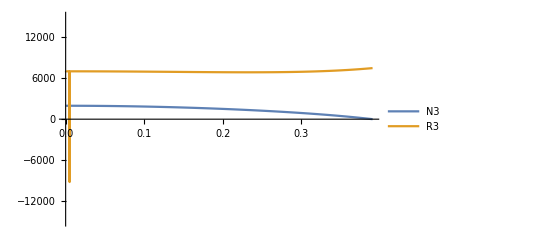

```mathematica
(*Grafico della normale del piano N3 e della tensione della fune R3*)
Plot[Evaluate[Simplify@Evaluate[{N3,R3}/.solR]/.sol],{t,0,Tmax},PlotRange->{-15000,15000},PlotLegends->{"N3","R3"}]
```

```mathematica
(*Condizioni finali della fase 1 che diventeranno le condizioni iniziali della fase 2*)
Cf={q1[Tmax],q1'[Tmax],q2[Tmax],q2'[Tmax],θ3[Tmax],θ3'[Tmax]}/.sol
```

{{2.79832,1.21505,-1.47173,0.352143,0.2659,1.423}}

```mathematica
(*Posizioni dei punti del trabucco in funzione del tempo*)
xAt[t_]:=Evaluate[xA/.sol]
yAt[t_]:=Evaluate[yA/.sol]
xDt[t_]:=Evaluate[xD/.sol]
yDt[t_]:=Evaluate[yD/.sol]
xCt[t_]:=Evaluate[xC/.sol]
yCt[t_]:=Evaluate[yC/.sol]
xBt[t_]:=Evaluate[xB/.sol]
yBt[t_]:=Evaluate[yB/.sol]
xG2t[t_]:=Evaluate[xG2/.sol]
yG2t[t_]:=Evaluate[yG2/.sol]
```

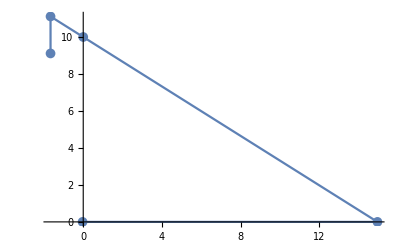

```mathematica
(*Configurazione iniziale all'istante t=0 *)
ListLinePlot[{{xDt[0][[1]],yDt[0][[1]]},{xCt[0][[1]],yCt[0][[1]]},{xAt[0][[1]],yAt[0][[1]]},{xBt[0][[1]],yBt[0][[1]]},{xG2t[0][[1]],yG2t[0][[1]]}},PlotMarkers->{"●",10}]
```

```mathematica
(*Animazione del movimento del trabucco nella configurazione 1*)
Animate[ListLinePlot[{{xDt[t][[1]],yDt[t][[1]]},{xCt[t][[1]],yCt[t][[1]]},{xAt[t][[1]],yAt[t][[1]]},{xBt[t][[1]],yBt[t][[1]]},{xG2t[t][[1]],yG2t[t][[1]]}},PlotRange->{{-10,20},{-10,20}},AspectRatio->1,PlotMarkers->{"●",10}],{t,0,Tmax}]
```

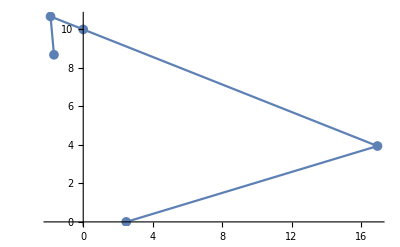

```mathematica
(*Configurazione finale della fase 1 all'istante t=Tmax *)
ListLinePlot[{{xDt[Tmax][[1]],yDt[Tmax][[1]]},{xCt[Tmax][[1]],yCt[Tmax][[1]]},{xAt[Tmax][[1]],yAt[Tmax][[1]]},{xBt[Tmax][[1]],yBt[Tmax][[1]]},{xG2t[Tmax][[1]],yG2t[Tmax][[1]]}},PlotMarkers->{"●",10}]
```

### f) Nel caso 2, ricavare le espressioni per le reazioni vincolari (ora manca la forza del suolo) ed esplicitare le 3 equazioni differenziali per i 3 gradi di libertà.

```mathematica
Clear[h,L,L1,L2,L3,m1,m2,m3,g,fc,IA]
```

```mathematica
(*Aggiungo il terzo grado di libertà*)
θ3[t_]:=q3[t]
(*Reazione vincolare del piano uguale a zero*)
N3=0;
```

```mathematica
(*Espressioni delle reazioni vincolari per la fase 2*)
solR2=Simplify@Solve[{N1y,N1x,N2x,N2y,N3y},{R1x,R1y,R2x,R2y,R3}]
```

{{R1x→g m3 Cot[q3[t]]+1/2 ((L m1-2 L1 (m1+m2)) Cos[q1[t]]+2 (L-L1) m3 Cot[q3[t]] Sin[q1[t]]) q1'[t]^2-L2 m2 Cos[q2[t]] q2'[t]^2+L3 m3 Cos[q3[t]] q3'[t]^2-L m3 Cos[q1[t]] Cot[q3[t]] q1''[t]+L1 m3 Cos[q1[t]] Cot[q3[t]] q1''[t]+1/2 L m1 Sin[q1[t]] q1''[t]-L1 m1 Sin[q1[t]] q1''[t]-L1 m2 Sin[q1[t]] q1''[t]-L2 m2 Sin[q2[t]] q2''[t]-L3 m3 Cos[q3[t]] Cot[q3[t]] q3''[t],R1y→g m1+g m2+g m3+1/2 (-2 L1 (m1+m2+m3)+L (m1+2 m3)) Sin[q1[t]] q1'[t]^2-L2 m2 Sin[q2[t]] q2'[t]^2+L3 m3 Sin[q3[t]] q3'[t]^2-1/2 L m1 Cos[q1[t]] q1''[t]+L1 m1 Cos[q1[t]] q1''[t]+L1 m2 Cos[q1[t]] q1''[t]-L m3 Cos[q1[t]] q1''[t]+L1 m3 Cos[q1[t]] q1''[t]+L2 m2 Cos[q2[t]] q2''[t]-L3 m3 Cos[q3[t]] q3''[t],R2x→-m2 (L1 Cos[q1[t]] q1'[t]^2+L2 Cos[q2[t]] q2'[t]^2+L1 Sin[q1[t]] q1''[t]+L2 Sin[q2[t]] q2''[t]),R2y→m2 (g-L1 Sin[q1[t]] q1'[t]^2-L2 Sin[q2[t]] q2'[t]^2+L1 Cos[q1[t]] q1''[t]+L2 Cos[q2[t]] q2''[t]),R3→m3 Csc[q3[t]] (g+(L-L1) Sin[q1[t]] q1'[t]^2+L3 Sin[q3[t]] q3'[t]^2-(L-L1) Cos[q1[t]] q1''[t]-L3 Cos[q3[t]] q3''[t])}}

```mathematica
E3GdL=Simplify[{E1,E2,N3x}/.solR2]
```

{{1/2 g L m1 Cos[q1[t]]+1/3 (L^2-3 L L1+3 L1^2) m1 q1''[t]+L m3 Cos[q1[t]] (g+(L-L1) Sin[q1[t]] q1'[t]^2+L3 Sin[q3[t]] q3'[t]^2-(L-L1) Cos[q1[t]] q1''[t]-L3 Cos[q3[t]] q3''[t])+L1 m3 Cot[q3[t]] Sin[q1[t]] (g+(L-L1) Sin[q1[t]] q1'[t]^2+L3 Sin[q3[t]] q3'[t]^2-(L-L1) Cos[q1[t]] q1''[t]-L3 Cos[q3[t]] q3''[t])==g L1 m1 Cos[q1[t]]+L1 m2 Cos[q1[t]] (g-L1 Sin[q1[t]] q1'[t]^2-L2 Sin[q2[t]] q2'[t]^2+L1 Cos[q1[t]] q1''[t]+L2 Cos[q2[t]] q2''[t])+L1 m2 Sin[q1[t]] (L1 Cos[q1[t]] q1'[t]^2+L2 Cos[q2[t]] q2'[t]^2+L1 Sin[q1[t]] q1''[t]+L2 Sin[q2[t]] q2''[t])+L1 m3 Cos[q1[t]] (g+(L-L1) Sin[q1[t]] q1'[t]^2+L3 Sin[q3[t]] q3'[t]^2-(L-L1) Cos[q1[t]] q1''[t]-L3 Cos[q3[t]] q3''[t])+L m3 Cot[q3[t]] Sin[q1[t]] (g+(L-L1) Sin[q1[t]] q1'[t]^2+L3 Sin[q3[t]] q3'[t]^2-(L-L1) Cos[q1[t]] q1''[t]-L3 Cos[q3[t]] q3''[t]),L2 m2 (12 g Cos[q2[t]]-12 L1 Sin[q1[t]-q2[t]] q1'[t]^2+12 L1 Cos[q1[t]-q2[t]] q1''[t]+13 L2 q2''[t])==0,m3 Csc[q3[t]] (g Cos[q3[t]]+(L-L1) Sin[q1[t]-q3[t]] q1'[t]^2-(L-L1) Cos[q1[t]-q3[t]] q1''[t]-L3 q3''[t])==0}}

```mathematica
(*3 equazioni differenziali per i 3 gradi di libertà del sistema*)
Simplify@Solve[{E3GdL[[1,1]],E3GdL[[1,2]],E3GdL[[1,3]]},{q1''[t],q2''[t],q3''[t]}]
```

{{q1''[t]→(-39 g L m1 Cos[q1[t]]+78 g L1 m1 Cos[q1[t]]+42 g L1 m2 Cos[q1[t]]-39 g L m3 Cos[q1[t]]+39 g L1 m3 Cos[q1[t]]-36 g L1 m2 Cos[q1[t]-2 q2[t]]+39 g L m3 Cos[q1[t]-2 q3[t]]-39 g L1 m3 Cos[q1[t]-2 q3[t]]+(36 L1^2 m2 Sin[2 (q1[t]-q2[t])]+39 (L-L1)^2 m3 Sin[2 (q1[t]-q3[t])]) q1'[t]^2+78 L1 L2 m2 Sin[q1[t]-q2[t]] q2'[t]^2+78 L L3 m3 Sin[q1[t]-q3[t]] q3'[t]^2-78 L1 L3 m3 Sin[q1[t]-q3[t]] q3'[t]^2)/(26 L^2 m1-78 L L1 m1+78 L1^2 m1-42 L1^2 m2-39 L^2 m3+78 L L1 m3-39 L1^2 m3+36 L1^2 m2 Cos[2 (q1[t]-q2[t])]+39 (L-L1)^2 m3 Cos[2 (q1[t]-q3[t])]),q2''[t]→-((6 (-3 g L L1 m1 Cos[2 q1[t]-q2[t]]+6 g L1^2 m1 Cos[2 q1[t]-q2[t]]+6 g L1^2 m2 Cos[2 q1[t]-q2[t]]-3 g L L1 m3 Cos[2 q1[t]-q2[t]]+3 g L1^2 m3 Cos[2 q1[t]-q2[t]]+4 g L^2 m1 Cos[q2[t]]-15 g L L1 m1 Cos[q2[t]]+18 g L1^2 m1 Cos[q2[t]]-6 g L1^2 m2 Cos[q2[t]]-6 g L^2 m3 Cos[q2[t]]+9 g L L1 m3 Cos[q2[t]]-3 g L1^2 m3 Cos[q2[t]]+3 g L^2 m3 Cos[2 q1[t]-q2[t]-2 q3[t]]-3 g L L1 m3 Cos[2 q1[t]-q2[t]-2 q3[t]]+3 g L L1 m3 Cos[q2[t]-2 q3[t]]-3 g L1^2 m3 Cos[q2[t]-2 q3[t]]+3 g L^2 m3 Cos[2 q1[t]+q2[t]-2 q3[t]]-6 g L L1 m3 Cos[2 q1[t]+q2[t]-2 q3[t]]+3 g L1^2 m3 Cos[2 q1[t]+q2[t]-2 q3[t]]+2 L1 ((6 L L1 (m1-m3)+3 L1^2 (-2 m1+2 m2+m3)+L^2 (-2 m1+3 m3)) Sin[q1[t]-q2[t]]+3 (L-L1)^2 m3 Sin[q1[t]+q2[t]-2 q3[t]]) q1'[t]^2+6 L1^2 L2 m2 Sin[2 (q1[t]-q2[t])] q2'[t]^2+6 L L1 L3 m3 Sin[2 q1[t]-q2[t]-q3[t]] q3'[t]^2-6 L1^2 L3 m3 Sin[2 q1[t]-q2[t]-q3[t]] q3'[t]^2+6 L L1 L3 m3 Sin[q2[t]-q3[t]] q3'[t]^2-6 L1^2 L3 m3 Sin[q2[t]-q3[t]] q3'[t]^2))/(L2 (26 L^2 m1-78 L L1 m1+78 L1^2 m1-42 L1^2 m2-39 L^2 m3+78 L L1 m3-39 L1^2 m3+36 L1^2 m2 Cos[2 (q1[t]-q2[t])]+39 (L-L1)^2 m3 Cos[2 (q1[t]-q3[t])]))),q3''[t]→(39 g L^2 m1 Cos[2 q1[t]-q3[t]]-117 g L L1 m1 Cos[2 q1[t]-q3[t]]+78 g L1^2 m1 Cos[2 q1[t]-q3[t]]-42 g L L1 m2 Cos[2 q1[t]-q3[t]]+42 g L1^2 m2 Cos[2 q1[t]-q3[t]]+78 g L^2 m3 Cos[2 q1[t]-q3[t]]-156 g L L1 m3 Cos[2 q1[t]-q3[t]]+78 g L1^2 m3 Cos[2 q1[t]-q3[t]]+36 g L L1 m2 Cos[2 q1[t]-2 q2[t]-q3[t]]+36 g L L1 m2 Cos[2 q2[t]-q3[t]]-36 g L1^2 m2 Cos[2 q2[t]-q3[t]]+91 g L^2 m1 Cos[q3[t]]-273 g L L1 m1 Cos[q3[t]]+234 g L1^2 m1 Cos[q3[t]]-42 g L L1 m2 Cos[q3[t]]-42 g L1^2 m2 Cos[q3[t]]-78 g L^2 m3 Cos[q3[t]]+156 g L L1 m3 Cos[q3[t]]-78 g L1^2 m3 Cos[q3[t]]+36 g L1^2 m2 Cos[2 q1[t]-2 q2[t]+q3[t]]-4 (L-L1) ((-13 L^2 (m1-3 m3)+39 L L1 (m1-2 m3)+3 L1^2 (-13 m1+7 m2+13 m3)) Sin[q1[t]-q3[t]]+18 L1^2 m2 Sin[q1[t]-2 q2[t]+q3[t]]) q1'[t]^2-156 (L-L1) L1 L2 m2 Cos[q1[t]-q3[t]] Sin[q1[t]-q2[t]] q2'[t]^2-78 L^2 L3 m3 Sin[2 (q1[t]-q3[t])] q3'[t]^2+156 L L1 L3 m3 Sin[2 (q1[t]-q3[t])] q3'[t]^2-78 L1^2 L3 m3 Sin[2 (q1[t]-q3[t])] q3'[t]^2)/(2 L3 (26 L^2 m1-78 L L1 m1+78 L1^2 m1-42 L1^2 m2-39 L^2 m3+78 L L1 m3-39 L1^2 m3+36 L1^2 m2 Cos[2 (q1[t]-q2[t])]+39 (L-L1)^2 m3 Cos[2 (q1[t]-q3[t])]))}}

### g ) Determinare le condizioni iniziali al momento del distacco (suggerimento ricavarle dalle condizioni finali del punto precedente) e integrare le equazioni. Terminare l’integrazione nel momento in cui la corda diventa lasca (l’asta CD va in compressione). Rappresentare graficamente la tensione della corda. Realizzare una animazione anche per la fase 2.

```mathematica
(*Condizioni iniziali per la fase 2*)
Ci2={q1[Tmax]== Cf[[1,1]],q1'[Tmax]== Cf[[1,2]],q2[Tmax]== Cf[[1,3]],q2'[Tmax]== Cf[[1,4]],θ3[Tmax]==Cf[[1,5]],θ3'[Tmax]==Cf[[1,6]]};
```

```mathematica
I1=1/12 m1 L^2;
I2=1/12 m2 L2^2;
(*Parametri*)
h=10;
L=20;
L1=2;
L2=2;
L3=15;
m1=5;
m2=10000;
m3=200;
g=9.8;
fc=0.2;
```

```mathematica
(*Sistema da integrare per ricavare le espressioni dei moventi*)
Sys2=E3GdL∪Ci2∪{WhenEvent[Evaluate[{R3/.solR2}[[1,1]]==0],"StopIntegration"]};
```

```mathematica
sol2=NDSolve[Sys2,{q1,q2,q3},{t,Tmax,10}]
```

{{q1→InterpolatingFunction[…],q2→InterpolatingFunction[…],q3→InterpolatingFunction[…]}}

```mathematica
(*Istante in cui la tensione della fune diventa lasca*)
Tf=sol2[[1,1,2,1,1,2]]
```

1.77795

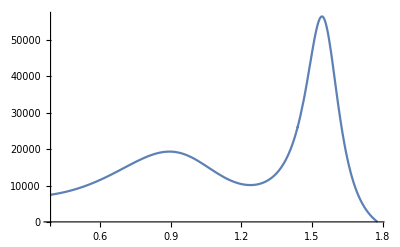

```mathematica
(*Grafico della tensione della fune nella fase 2*)
Plot[Evaluate[Simplify@Evaluate[R3/.solR2/.sol2]],{t,0.391,Tf},PlotRange->All]
```

```mathematica
xAt2[t_]:=Evaluate[xA/.sol2]
yAt2[t_]:=Evaluate[yA/.sol2]
xDt2[t_]:=Evaluate[xD/.sol2]
yDt2[t_]:=Evaluate[yD/.sol2]
xCt2[t_]:=Evaluate[xC/.sol2]
yCt2[t_]:=Evaluate[yC/.sol2]
xBt2[t_]:=Evaluate[xB/.sol2]
yBt2[t_]:=Evaluate[yB/.sol2]
xG2t2[t_]:=Evaluate[xG2/.sol2]
yG2t2[t_]:=Evaluate[yG2/.sol2]
```

```mathematica
(*Animazione del movimento del trabucco nella configurazione 2*)
Animate[ListLinePlot[{{xDt2[t][[1]],yDt2[t][[1]]},{xCt2[t][[1]],yCt2[t][[1]]},{xAt2[t][[1]],yAt2[t][[1]]},{xBt2[t][[1]],yBt2[t][[1]]},{xG2t2[t][[1]],yG2t2[t][[1]]}},PlotRange->{{-10,30},{-10,40}},AspectRatio->1,PlotMarkers->{"●",10}],{t,Tmax,Tf}]
```

### h) Calcolare la gittata che si avrebbe rilasciando la massa m3 ad un tempo t generico (suggerimento usare le formule della Fisica 1) e determinare l’istante in cui la gittata è massima e il valore di gittata ottenuta (FindMaximum).

```mathematica
(*Tempo di volo (calcolato con formula approssimata)*)
Tv=2(D[yG3, t])/g
```

0.204082 (-18 Cos[q1[t]] q1'[t]-15 Cos[q3[t]] q3'[t])

```mathematica
(*Gittata*)
G=(D[xG3, t])Tv
```

0.204082 (-18 Cos[q1[t]] q1'[t]-15 Cos[q3[t]] q3'[t]) (18 Sin[q1[t]] q1'[t]+15 Sin[q3[t]] q3'[t])

```mathematica
FG[t_]:=Evaluate[G/.sol2]
```

```mathematica
(*Istante in cui la gittata è massima nel verso positivo di x e valore della gittata*)
FindMaximum[FG[t],{t,Tmax,Tf},AccuracyGoal->6,PrecisionGoal->10]
```

{211.659,{t→1.12756}}

```mathematica
(*Istante in cui la gittata è massima nel verso negativo di x e valore della gittata*)
FindMinimum[FG[t],{t,1.1275578147905971},AccuracyGoal->6,PrecisionGoal->10]
```

{-129.85,{t→1.62667}}

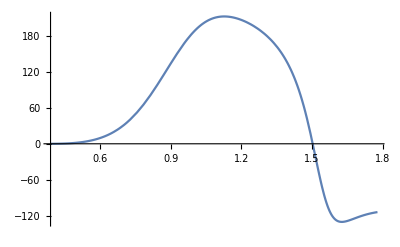

```mathematica
(*Grafico della gittata del proiettile*)
Plot[FG[t],{t,Tmax,Tf},PlotRange->All]
```

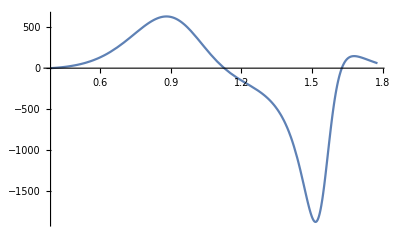

```mathematica
(*Grafico della derivata della gittata del proiettile in cui gli zeri sono gli istanti (t->1.1275578147905971) in cui è massima la gittata nel verso positivo x e (t->1.626669409899428)in cui è massima la gittata nel verso negativo x*)
Plot[FG'[t],{t,Tmax,Tf},PlotRange->All]
```

### i) Provare con diversi valori della massa m3 a massimizzare la gittata .

#### Prova 1 (m3=20)

```mathematica
Clear[m3,N3]
m3=20;
θ3[t_]:=ArcSin[(h+(-L+L1) Sin[q1[t]])/L3]
```

```mathematica
(*Reazioni vincolari e accelerazioni iniziali*)
Simplify@Solve[{N1x,N1y,E1,N2x,N2y,E2,N3x,N3y}/.t->0/.q2[0]-> - π/2/.q2'[0]-> 0/.q1[0]->π-ArcSin[h/(L-L1)]/.q1'[0]-> 0,{R1x,R1y,R2x,R2y,R3,N3,q1''[0],q2''[0]}]
```

{{R1x→-3368.17,R1y→8639.06,R2x→-4604.56,R2y→8410.88,R3→1116.67,N3→196.,q1''[0]→5.38733,q2''[0]→2.76273}}

```mathematica
Sys=E2GdL∪Ci∪{WhenEvent[Evaluate[{N3/.solR}[[1,1]]==0],"StopIntegration"]};
sol=NDSolve[Sys,{q1,q2},{t,0,10}]
```

{{q1→InterpolatingFunction[…],q2→InterpolatingFunction[…]}}

```mathematica
(*Istante in cui la normale del piano N3 è uguale a zero*)
Tmax=sol[[1,1,2,1,1,2]]
```

0.25464

```mathematica
(*Condizioni finali della fase 1 che diventeranno le condizioni iniziali della fase 2*)
Cf={q1[Tmax],q1'[Tmax],q2[Tmax],q2'[Tmax],θ3[Tmax],θ3'[Tmax]}/.sol
```

{{2.72317,1.30648,-1.49495,0.489291,0.180051,1.45606}}

```mathematica
Ci2={q1[Tmax]== Cf[[1,1]],q1'[Tmax]== Cf[[1,2]],q2[Tmax]== Cf[[1,3]],q2'[Tmax]== Cf[[1,4]],θ3[Tmax]==Cf[[1,5]],θ3'[Tmax]==Cf[[1,6]]};
```

```mathematica
θ3[t_]:=q3[t]
```

```mathematica
Sys2=E3GdL∪Ci2∪{WhenEvent[Evaluate[{R3/.solR2}[[1,1]]==0],"StopIntegration"]};
sol3=NDSolve[Sys2,{q1,q2,q3},{t,Tmax,10}]
```

{{q1→InterpolatingFunction[…],q2→InterpolatingFunction[…],q3→InterpolatingFunction[…]}}

```mathematica
Tf=sol3[[1,1,2,1,1,2]]
```

0.860733

```mathematica
FG1[t_]:=Evaluate[G/.sol3]
(*Istante in cui la gittata è massima nel verso positivo di x e valore della gittata*)
FindMaximum[FG1[t],{t,Tmax,Tf},AccuracyGoal->6,PrecisionGoal->10]
```

{380.385,{t→0.694893}}

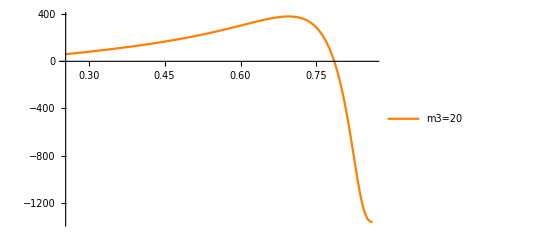

```mathematica
(*Grafico della gittata del proiettile*)
P1=Plot[FG1[t],{t,Tmax,Tf},PlotRange->All,PlotStyle->Orange,PlotLegends->{"m3=20"}]
```

#### Prova 2 (m3=50)

```mathematica
Clear[m3,N3]
m3=50;
θ3[t_]:=ArcSin[(h+(-L+L1) Sin[q1[t]])/L3]
```

```mathematica
(*Reazioni vincolari e accelerazioni iniziali*)
Simplify@Solve[{N1x,N1y,E1,N2x,N2y,E2,N3x,N3y}/.t->0/.q2[0]-> - π/2/.q2'[0]-> 0/.q1[0]->π-ArcSin[h/(L-L1)]/.q1'[0]-> 0,{R1x,R1y,R2x,R2y,R3,N3,q1''[0],q2''[0]}]
```

{{R1x→-1525.01,R1y→17033.1,R2x→-4172.27,R2y→16821.8,R3→2538.78,N3→490.,q1''[0]→4.88155,q2''[0]→2.50336}}

```mathematica
Sys=E2GdL∪Ci∪{WhenEvent[Evaluate[{N3/.solR}[[1,1]]==0],"StopIntegration"]};
sol=NDSolve[Sys,{q1,q2},{t,0,10}]
```

{{q1→InterpolatingFunction[…],q2→InterpolatingFunction[…]}}

```mathematica
(*Istante in cui la normale del piano N3 è uguale a zero*)
Tmax=sol[[1,1,2,1,1,2]]
```

0.277701

```mathematica
(*Condizioni finali della fase 1 che diventeranno le condizioni iniziali della fase 2*)
Cf={q1[Tmax],q1'[Tmax],q2[Tmax],q2'[Tmax],θ3[Tmax],θ3'[Tmax]}/.sol
```

{{2.73652,1.29056,-1.49026,0.465536,0.194992,1.45084}}

```mathematica
Ci2={q1[Tmax]== Cf[[1,1]],q1'[Tmax]== Cf[[1,2]],q2[Tmax]== Cf[[1,3]],q2'[Tmax]== Cf[[1,4]],θ3[Tmax]==Cf[[1,5]],θ3'[Tmax]==Cf[[1,6]]};
```

```mathematica
θ3[t_]:=q3[t]
```

```mathematica
Sys2=E3GdL∪Ci2∪{WhenEvent[Evaluate[{R3/.solR2}[[1,1]]==0],"StopIntegration"]};
sol3=NDSolve[Sys2,{q1,q2,q3},{t,Tmax,10}]
```

{{q1→InterpolatingFunction[…],q2→InterpolatingFunction[…],q3→InterpolatingFunction[…]}}

```mathematica
Tf=sol3[[1,1,2,1,1,2]]
```

1.37563

```mathematica
FG2[t_]:=Evaluate[G/.sol3]
```

```mathematica
(*Istante in cui la gittata è massima nel verso positivo di x e valore della gittata*)
FindMaximum[FG2[t],{t,Tmax,Tf},AccuracyGoal->6,PrecisionGoal->10]
```

{310.673,{t→0.75285}}

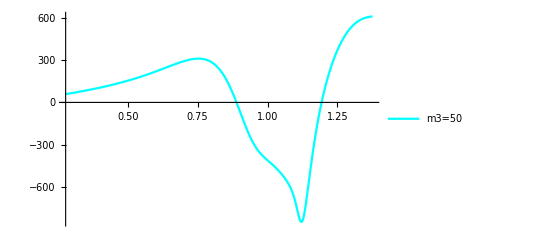

```mathematica
(*Grafico della gittata del proiettile*)
P2=Plot[FG2[t],{t,Tmax,Tf},PlotRange->All,PlotStyle->Cyan,PlotLegends->{"m3=50"}]
```

#### Prova 3 (m3=100)

```mathematica
Clear[m3,N3]
m3=100;
θ3[t_]:=ArcSin[(h+(-L+L1) Sin[q1[t]])/L3]
```

```mathematica
(*Reazioni vincolari e accelerazioni iniziali*)
Simplify@Solve[{N1x,N1y,E1,N2x,N2y,E2,N3x,N3y}/.t->0/.q2[0]-> - π/2/.q2'[0]-> 0/.q1[0]->π-ArcSin[h/(L-L1)]/.q1'[0]-> 0,{R1x,R1y,R2x,R2y,R3,N3,q1''[0],q2''[0]}]
```

{{R1x→902.188,R1y→28087.,R2x→-3603.,R2y→27897.8,R3→4411.51,N3→980.,q1''[0]→4.21551,q2''[0]→2.1618}}

```mathematica
Sys=E2GdL∪Ci∪{WhenEvent[Evaluate[{N3/.solR}[[1,1]]==0],"StopIntegration"]};
sol=NDSolve[Sys,{q1,q2},{t,0,10}]
```

{{q1→InterpolatingFunction[…],q2→InterpolatingFunction[…]}}

```mathematica
(*Istante in cui la normale del piano N3 è uguale a zero*)
Tmax=sol[[1,1,2,1,1,2]]
```

0.315699

```mathematica
(*Condizioni finali della fase 1 che diventeranno le condizioni iniziali della fase 2*)
Cf={q1[Tmax],q1'[Tmax],q2[Tmax],q2'[Tmax],θ3[Tmax],θ3'[Tmax]}/.sol
```

{{2.75795,1.26472,-1.48321,0.426819,0.219264,1.44186}}

```mathematica
Ci2={q1[Tmax]== Cf[[1,1]],q1'[Tmax]== Cf[[1,2]],q2[Tmax]== Cf[[1,3]],q2'[Tmax]== Cf[[1,4]],θ3[Tmax]==Cf[[1,5]],θ3'[Tmax]==Cf[[1,6]]};
```

```mathematica
θ3[t_]:=q3[t]
```

```mathematica
Sys2=E3GdL∪Ci2∪{WhenEvent[Evaluate[{R3/.solR2}[[1,1]]==0],"StopIntegration"]};
sol3=NDSolve[Sys2,{q1,q2,q3},{t,Tmax,10}]
```

{{q1→InterpolatingFunction[…],q2→InterpolatingFunction[…],q3→InterpolatingFunction[…]}}

```mathematica
Tf=sol3[[1,1,2,1,1,2]]
```

1.54556

```mathematica
FG3[t_]:=Evaluate[G/.sol3]
```

```mathematica
(*Istante in cui la gittata è massima nel verso positivo di x e valore della gittata*)
FindMaximum[FG3[t],{t,Tmax,Tf},AccuracyGoal->6,PrecisionGoal->10]
```

{238.581,{t→0.839208}}

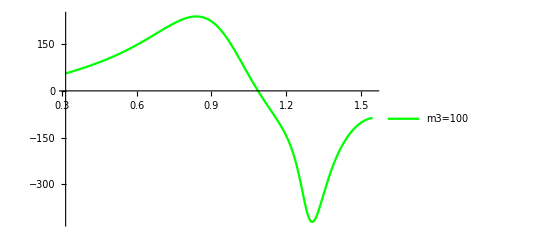

```mathematica
(*Grafico della gittata del proiettile*)
P3=Plot[FG3[t],{t,Tmax,Tf},PlotRange->All,PlotStyle->Green,PlotLegends->{"m3=100"}]
```

#### Prova 4 (m3=300)

```mathematica
Clear[m3,N3]
m3=300;
θ3[t_]:=ArcSin[(h+(-L+L1) Sin[q1[t]])/L3]
```

```mathematica
(*Reazioni vincolari e accelerazioni iniziali*)
Simplify@Solve[{N1x,N1y,E1,N2x,N2y,E2,N3x,N3y}/.t->0/.q2[0]-> - π/2/.q2'[0]-> 0/.q1[0]->π-ArcSin[h/(L-L1)]/.q1'[0]-> 0,{R1x,R1y,R2x,R2y,R3,N3,q1''[0],q2''[0]}]
```

{{R1x→6434.61,R1y→53282.5,R2x→-2305.45,R2y→53143.8,R3→8680.12,N3→2940.,q1''[0]→2.69737,q2''[0]→1.38327}}

```mathematica
Sys=E2GdL∪Ci∪{WhenEvent[Evaluate[{N3/.solR}[[1,1]]==0],"StopIntegration"]};
sol=NDSolve[Sys,{q1,q2},{t,0,10}]
```

{{q1→InterpolatingFunction[…],q2→InterpolatingFunction[…]}}

```mathematica
(*Istante in cui la normale del piano N3 è uguale a zero*)
Tmax=sol[[1,1,2,1,1,2]]
```

0.46425

```mathematica
(*Condizioni finali della fase 1 che diventeranno le condizioni iniziali della fase 2*)
Cf={q1[Tmax],q1'[Tmax],q2[Tmax],q2'[Tmax],θ3[Tmax],θ3'[Tmax]}/.sol
```

{{2.83603,1.16738,-1.46338,0.280526,0.310637,1.40312}}

```mathematica
Ci2={q1[Tmax]== Cf[[1,1]],q1'[Tmax]== Cf[[1,2]],q2[Tmax]== Cf[[1,3]],q2'[Tmax]== Cf[[1,4]],θ3[Tmax]==Cf[[1,5]],θ3'[Tmax]==Cf[[1,6]]};
```

```mathematica
θ3[t_]:=q3[t]
```

```mathematica
Sys2=E3GdL∪Ci2∪{WhenEvent[Evaluate[{R3/.solR2}[[1,1]]==0],"StopIntegration"]};
sol3=NDSolve[Sys2,{q1,q2,q3},{t,Tmax,10}]
```

{{q1→InterpolatingFunction[…],q2→InterpolatingFunction[…],q3→InterpolatingFunction[…]}}

```mathematica
Tf=sol3[[1,1,2,1,1,2]]
```

1.92527

```mathematica
FG4[t_]:=Evaluate[G/.sol3]
(*Istante in cui la gittata è massima nel verso positivo di x e valore della gittata*)
FindMaximum[FG4[t],{t,Tmax,Tf},AccuracyGoal->6,PrecisionGoal->10]
```

{122.158,{t→1.11338}}

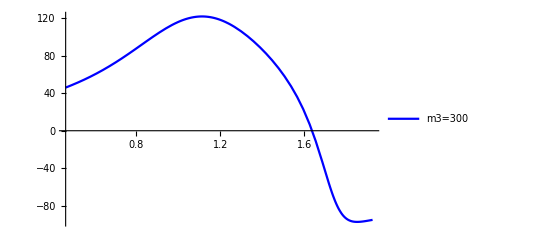

```mathematica
(*Grafico della gittata del proiettile*)
P4=Plot[FG4[t],{t,Tmax,Tf},PlotRange->All,PlotStyle->Blue,PlotLegends->{"m3=300"}]
```

#### Prova 5 (m3=40)

```mathematica
Clear[m3,N3]
m3=40;
θ3[t_]:=ArcSin[(h+(-L+L1) Sin[q1[t]])/L3]
```

```mathematica
(*Reazioni vincolari e accelerazioni iniziali*)
Simplify@Solve[{N1x,N1y,E1,N2x,N2y,E2,N3x,N3y}/.t->0/.q2[0]-> - π/2/.q2'[0]-> 0/.q1[0]->π-ArcSin[h/(L-L1)]/.q1'[0]-> 0,{R1x,R1y,R2x,R2y,R3,N3,q1''[0],q2''[0]}]
```

{{R1x→-2101.14,R1y→14409.3,R2x→-4307.39,R2y→14192.7,R3→2094.26,N3→392.,q1''[0]→5.03965,q2''[0]→2.58444}}

```mathematica
Sys=E2GdL∪Ci∪{WhenEvent[Evaluate[{N3/.solR}[[1,1]]==0],"StopIntegration"]};
sol=NDSolve[Sys,{q1,q2},{t,0,10}]
```

{{q1→InterpolatingFunction[…],q2→InterpolatingFunction[…]}}

```mathematica
(*Istante in cui la normale del piano N3 è uguale a zero*)
Tmax=sol[[1,1,2,1,1,2]]
```

0.270038

```mathematica
(*Condizioni finali della fase 1 che diventeranno le condizioni iniziali della fase 2*)
Cf={q1[Tmax],q1'[Tmax],q2[Tmax],q2'[Tmax],θ3[Tmax],θ3'[Tmax]}/.sol
```

{{2.73211,1.29583,-1.49178,0.473407,0.190046,1.45259}}

```mathematica
Ci2={q1[Tmax]== Cf[[1,1]],q1'[Tmax]== Cf[[1,2]],q2[Tmax]== Cf[[1,3]],q2'[Tmax]== Cf[[1,4]],θ3[Tmax]==Cf[[1,5]],θ3'[Tmax]==Cf[[1,6]]};
```

```mathematica
θ3[t_]:=q3[t]
```

```mathematica
Sys2=E3GdL∪Ci2∪{WhenEvent[Evaluate[{R3/.solR2}[[1,1]]==0],"StopIntegration"]};
sol3=NDSolve[Sys2,{q1,q2,q3},{t,Tmax,10}]
```

{{q1→InterpolatingFunction[…],q2→InterpolatingFunction[…],q3→InterpolatingFunction[…]}}

```mathematica
Tf=sol3[[1,1,2,1,1,2]]
```

1.31837

```mathematica
FG5[t_]:=Evaluate[G/.sol3]
(*Istante in cui la gittata è massima nel verso positivo di x e valore della gittata*)
FindMaximum[FG5[t],{t,Tmax,Tf},AccuracyGoal->6,PrecisionGoal->10]
```

{330.807,{t→0.734139}}

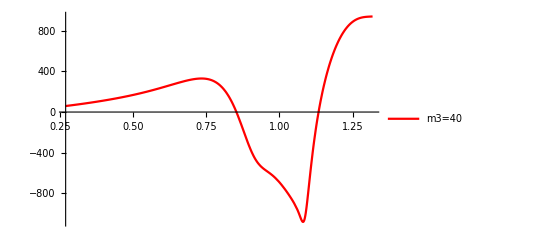

```mathematica
(*Grafico della gittata del proiettile*)
P5=Plot[FG5[t],{t,Tmax,Tf},PlotRange->All,PlotStyle->Red,PlotLegends->{"m3=40"}]
```

#### Confronto

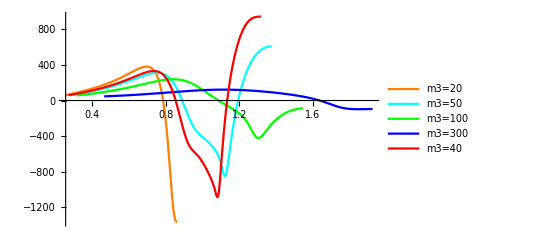

```mathematica
(*Grafici della gittata del proiettile con diversi valori di m3*)
Show[{P1,P2,P3,P4,P5},PlotRange->All]
```

```mathematica
(*Provando con diversi valori della massa m3 si nota che la gittata, sia nel verso positivo che nel verso negativo di x, aumenta al diminuire di m3. La gittata massima si ottiene quando m3 tende a zero*)
```